```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\mouze\Desktop\CM_labs\lab4

```mathematica
runge4u =Import["runge4_u.txt","Table"][[1]]
runge4c =Import["runge4_c.txt","Table"][[1]]
runge8u =Import["runge8_u.txt","Table"][[1]]
runge8c =Import["runge8_c.txt","Table"][[1]]
runge16u =Import["runge16_u.txt","Table"][[1]]
runge16c =Import["runge16_c.txt","Table"][[1]]
runge32u =Import["runge32_u.txt","Table"][[1]]
runge32c =Import["runge32_c.txt","Table"][[1]]
```

{3.31565,0,-4.27719,-2.22045×10^-16,1}

{2.7465,4.44089×10^-16,-3.54298,0,1}

{53.6893,0,-102.815,2.13163×10^-14,61.3672,0,-13.203,-2.77556×10^-16,1}

{17.6203,-1.06581×10^-14,-40.3504,3.55271×10^-15,31.3482,-8.88178×10^-15,-9.51343,3.33067×10^-16,1}

{15403.1,-9.09495×10^-12,-49713.5,-2.91038×10^-11,63743.8,6.91216×10^-11,-41870,-2.18279×10^-11,15206.7,-5.72982×10^-11,-3100.35,-1.31308×10^-11,351.984,-1.39266×10^-12,-22.7759,-2.19547×10^-14,1}

{895.603,1.13687×10^-13,-3842.14,3.18323×10^-12,6814.73,2.59206×10^-11,-6457.85,5.32054×10^-11,3529.36,1.25056×10^-12,-1122.49,-4.0643×10^-12,201.018,-3.30758×10^-12,-19.192,-5.34045×10^-13,1}

{1.24654×10^9,3.57628×10^-6,-7.33435×10^9,-0.0000143051,1.92587×10^10,-0.000209808,-2.98488×10^10,0.00146866,3.04414×10^10,-0.0000419617,-2.15673×10^10,-0.000136375,1.09293×10^10,-0.000498772,-4.02131×10^9,-0.0000325441,1.08063×10^9,0.0000564158,-2.12025×10^8,0.000093285,3.02548×10^7,-0.0000170094,-3.12876×10^6,-0.0000115023,235672,-3.88967×10^-6,-13317.6,-7.49804×10^-7,607.737,-4.29536×10^-8,-24.9599,-3.05666×10^-10,1}

{2.44034×10^6,-6.98492×10^-9,-2.02304×10^7,-1.93715×10^-7,7.63072×10^7,-2.87592×10^-6,-1.73342×10^8,-9.64105×10^-6,2.64571×10^8,-0.0000507832,-2.86622×10^8,-0.000124589,2.27014×10^8,-0.000143453,-1.33436×10^8,-0.0000115335,5.84994×10^7,0.000122953,-1.90761×10^7,0.0000894889,4.58326×10^6,0.000011422,-798984,2.24981×10^-6,99143.8,0.0000315476,-8616.98,0.0000214505,528.281,3.84088×10^-6,-24.5312,1.42818×10^-7,1}

```mathematica
runge4u
```

{{1.85185,0,-2.68519,-2.22045×10^-16,1}}

```mathematica
poly4u = ∑_(k=1)^(Length@runge4u) runge4u[[k]]*x^(Length@runge4u-k)
poly4c = ∑_(k=1)^(Length@runge4c) runge4c[[k]]*x^(Length@runge4c-k)
```

1-2.22045×10^-16 x-4.27719 x^2+3.31565 x^4

1-3.54298 x^2+4.44089×10^-16 x^3+2.7465 x^4

```mathematica
poly4u /. x->-1
```

0.16666

```mathematica
poly8u = ∑_(k=1)^(Length@runge8u) runge8u[[k]]*x^(Length@runge8u-k)
poly8c = ∑_(k=1)^(Length@runge8c) runge8c[[k]]*x^(Length@runge8c-k)
```

1-2.77556×10^-16 x-13.203 x^2+61.3672 x^4+2.13163×10^-14 x^5-102.815 x^6+53.6893 x^8

1+3.33067×10^-16 x-9.51343 x^2-8.88178×10^-15 x^3+31.3482 x^4+3.55271×10^-15 x^5-40.3504 x^6-1.06581×10^-14 x^7+17.6203 x^8

```mathematica
poly16u = ∑_(k=1)^(Length@runge16u) runge16u[[k]]*x^(Length@runge16u-k)
poly16c = ∑_(k=1)^(Length@runge16c) runge16c[[k]]*x^(Length@runge16c-k)
```

1-2.19547×10^-14 x-22.7759 x^2-1.39266×10^-12 x^3+351.984 x^4-1.31308×10^-11 x^5-3100.35 x^6-5.72982×10^-11 x^7+15206.7 x^8-2.18279×10^-11 x^9-41870 x^10+6.91216×10^-11 x^11+63743.8 x^12-2.91038×10^-11 x^13-49713.5 x^14-9.09495×10^-12 x^15+15403.1 x^16

1-5.34045×10^-13 x-19.192 x^2-3.30758×10^-12 x^3+201.018 x^4-4.0643×10^-12 x^5-1122.49 x^6+1.25056×10^-12 x^7+3529.36 x^8+5.32054×10^-11 x^9-6457.85 x^10+2.59206×10^-11 x^11+6814.73 x^12+3.18323×10^-12 x^13-3842.14 x^14+1.13687×10^-13 x^15+895.603 x^16

```mathematica
poly32u = ∑_(k=1)^(Length@runge32u) runge32u[[k]]*x^(Length@runge32u-k)
poly32c = ∑_(k=1)^(Length@runge32c) runge32c[[k]]*x^(Length@runge32c-k)
```

1-3.05666×10^-10 x-24.9599 x^2-4.29536×10^-8 x^3+607.737 x^4-7.49804×10^-7 x^5-13317.6 x^6-3.88967×10^-6 x^7+235672 x^8-0.0000115023 x^9-3.12876×10^6 x^10-0.0000170094 x^11+3.02548×10^7 x^12+0.000093285 x^13-2.12025×10^8 x^14+0.0000564158 x^15+1.08063×10^9 x^16-0.0000325441 x^17-4.02131×10^9 x^18-0.000498772 x^19+1.09293×10^10 x^20-0.000136375 x^21-2.15673×10^10 x^22-0.0000419617 x^23+3.04414×10^10 x^24+0.00146866 x^25-2.98488×10^10 x^26-0.000209808 x^27+1.92587×10^10 x^28-0.0000143051 x^29-7.33435×10^9 x^30+3.57628×10^-6 x^31+1.24654×10^9 x^32

1+1.42818×10^-7 x-24.5312 x^2+3.84088×10^-6 x^3+528.281 x^4+0.0000214505 x^5-8616.98 x^6+0.0000315476 x^7+99143.8 x^8+2.24981×10^-6 x^9-798984 x^10+0.000011422 x^11+4.58326×10^6 x^12+0.0000894889 x^13-1.90761×10^7 x^14+0.000122953 x^15+5.84994×10^7 x^16-0.0000115335 x^17-1.33436×10^8 x^18-0.000143453 x^19+2.27014×10^8 x^20-0.000124589 x^21-2.86622×10^8 x^22-0.0000507832 x^23+2.64571×10^8 x^24-9.64105×10^-6 x^25-1.73342×10^8 x^26-2.87592×10^-6 x^27+7.63072×10^7 x^28-1.93715×10^-7 x^29-2.02304×10^7 x^30-6.98492×10^-9 x^31+2.44034×10^6 x^32

```mathematica
f=  1/(1+25x^2)
```

1/(1+25 x^2)

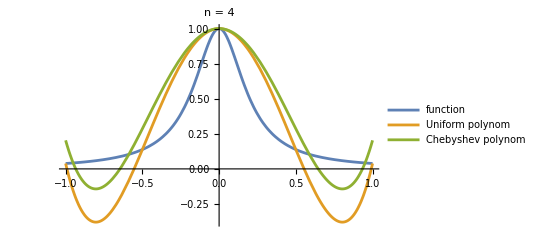

```mathematica
Plot[{f, poly4u, poly4c},{x,-1,1},PlotLegends->{"function","Uniform polynom", "Chebyshev polynom"},PlotLabel->"n = 4"]
```

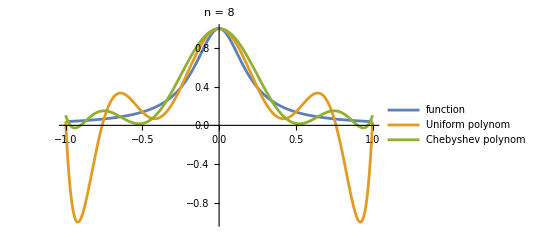

```mathematica
Plot[{f, poly8u, poly8c},{x,-1,1},PlotLegends->{"function","Uniform polynom", "Chebyshev polynom"},PlotLabel->"n = 8"]
```

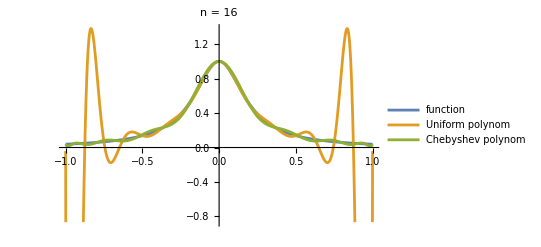

```mathematica
Plot[{f, poly16u, poly16c},{x,-1,1},PlotLegends->{"function","Uniform polynom", "Chebyshev polynom"},PlotLabel->"n = 16"]
```

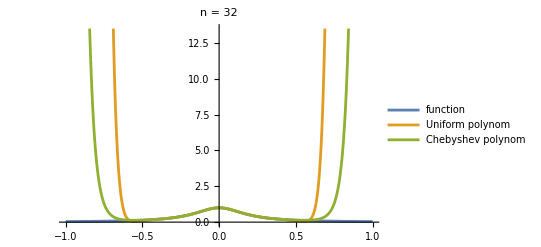

```mathematica
Plot[{f, poly32u, poly32c},{x,-1,1},PlotLegends->{"function","Uniform polynom", "Chebyshev polynom"},PlotLabel->"n = 32"]
```